```mathematica
n=1000;
```

```mathematica
h=Table[If[i==j,2-1/(25j),0],{i,n},{j,n}];
```

```mathematica
k=Table[If[i==j+1,-1,0],{i,n},{j,n}];
```

```mathematica
m=Table[If[i==j-1,-1,0],{i,n},{j,n}];
```

```mathematica
p=Table[h[[i,j]]+k[[i,j]]+m[[i,j]],{i,n},{j,n}];
```

```mathematica
eig=Eigenvalues[N[p]];
```

```mathematica
eve=Eigenvectors[N[p]];
```

```mathematica
En=TakeSmallest[eig,3]
```

{-0.00039996,-0.0000999873,-0.0000399639}

```mathematica
2500*En
```

{-0.9999,-0.249968,-0.0999098}

```mathematica
Ordering[eig,3]
```

{994,997,999}

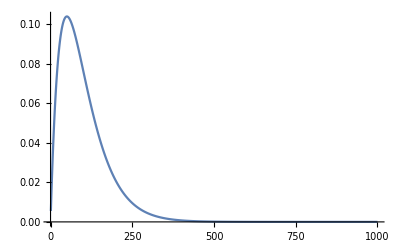

```mathematica
ListLinePlot[eve[[994]],PlotRange->Full]
```

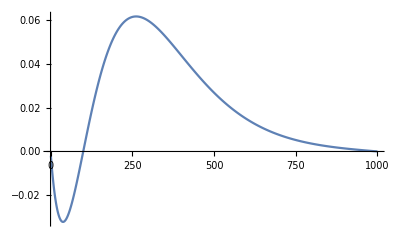

```mathematica
ListLinePlot[eve[[997]],PlotRange->Full]
```

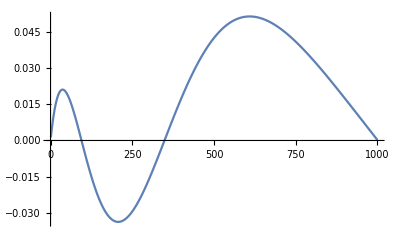

```mathematica
ListLinePlot[eve[[999]],PlotRange->Full]
```

```mathematica
h=Table[If[i==j,2-1/(25j)+2/j^2,0],{i,n},{j,n}];
```

```mathematica
k=Table[If[i==j+1,-1,0],{i,n},{j,n}];
```

```mathematica
m=Table[If[i==j-1,-1,0],{i,n},{j,n}];
```

```mathematica
p=Table[h[[i,j]]+k[[i,j]]+m[[i,j]],{i,n},{j,n}];
```

```mathematica
eig=Eigenvalues[N[p]];
```

```mathematica
eve=Eigenvectors[N[p]];
```

```mathematica
En=TakeSmallest[eig,3];
```

```mathematica
2500*En
```

{-0.249991,-0.103278,0.0158618}

```mathematica
Ordering[eig,3]
```

{997,999,1000}

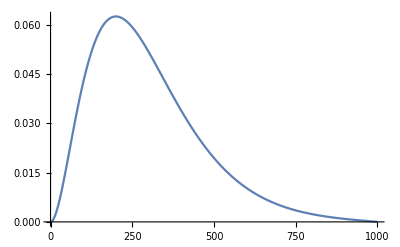

```mathematica
ListLinePlot[eve[[997]],PlotRange->Full]
```

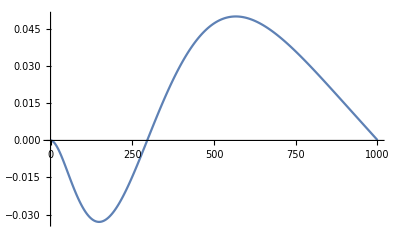

```mathematica
ListLinePlot[eve[[999]],PlotRange->Full]
```

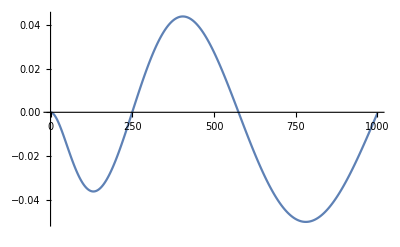

```mathematica
ListLinePlot[eve[[1000]],PlotRange->Full]
```

```mathematica
h=Table[If[i==j,2-1/(25j)+6/j^2,0],{i,n},{j,n}];
```

```mathematica
k=Table[If[i==j+1,-1,0],{i,n},{j,n}];
```

```mathematica
m=Table[If[i==j-1,-1,0],{i,n},{j,n}];
```

```mathematica
p=Table[h[[i,j]]+k[[i,j]]+m[[i,j]],{i,n},{j,n}];
```

```mathematica
eig=Eigenvalues[N[p]];
```

```mathematica
eve=Eigenvectors[N[p]];
```

```mathematica
En=TakeSmallest[eig,3];
```

```mathematica
2500*En
```

{-0.107958,-0.0112765,0.135962}

```mathematica
Ordering[eig,3]
```

{999,1000,998}

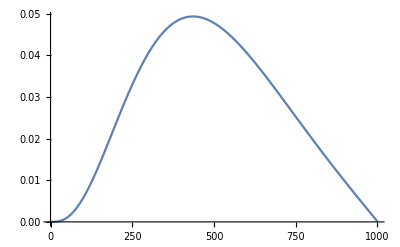

```mathematica
ListLinePlot[eve[[999]],PlotRange->Full]
```

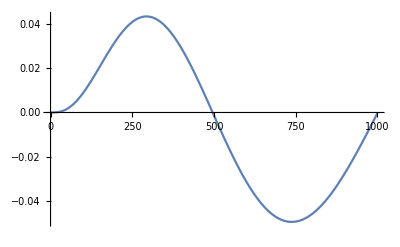

```mathematica
ListLinePlot[eve[[1000]],PlotRange->Full]
```

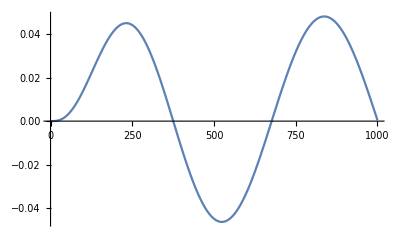

```mathematica
ListLinePlot[eve[[998]],PlotRange->Full]
```